## Testpolygon (without import)

{5,5,5}

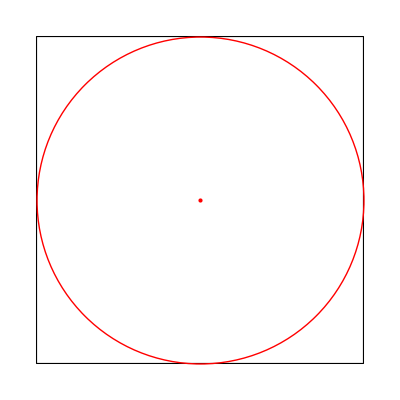

```mathematica
poly = Polygon @ {{0, 0}, {10, 0}, {10, 10}, {0, 10}};
dsk = Disk[{x, y}, r];
sol = Quiet @ ArgMax[{r, RegionWithin[poly, dsk]}, {x, y, r}] 
Graphics[{EdgeForm[Black], FaceForm[White], poly, 
   Red, Circle[Most @ sol, Last @sol], PointSize[Large], Point[Most @ sol]}]
```

## Polygon (with import points from file)

```mathematica
Clear["Global`*"]
data = Drop[Import["polygon.txt", "Table"], -1];
data1 = {{59.9798,310.193},{15.625,491.213},{16.6331,515.817},{29.7379,565.026},{66.0282,654.657},{87.1976,688.049},{177.923,830.404},{233.367,895.431},{248.488,905.975},{320.061,942.882},{405.746,974.517},{521.673,993.849},{618.448,949.912},{660.786,927.065},{681.956,913.005},{866.432,688.049},{929.94,591.388},{929.94,498.243},{912.802,392.794},{887.601,311.951},{832.157,192.443},{732.359,72.935},{690.02,50.0879},{630.544,21.9684},{597.278,11.4236},{524.698,16.696},{482.359,21.9684},{456.149,27.2408},{424.899,34.2707},{346.27,55.3603},{295.867,74.6924},{239.415,97.5395},{179.94,127.417},{128.528,167.838},{103.327,206.503},{85.1815,243.41},{67.0363,283.831}};
polygon = Polygon @ data1;
largestCricle = Disk[{x, y}, r];
pointAndRadius = Quiet @ ArgMax[{r, RegionWithin[polygon, largestCricle]}, {x, y, r}]
Graphics[{EdgeForm[Black], FaceForm[White], polygon, 
   Red, Circle[Most @ pointAndRadius, Last @pointAndRadius], PointSize[Large], Point[Most @ pointAndRadius]}]
```

{472.571,476.664,438.592}

-Graphics-

--> sollte mit data und data1 gleiche identische listen, aber mit data funktioniert ArgMax nicht (aber mit data1 schon)